# Cuaderno de Prácticas

## Análisis y métodos numéricos

## Grado en Ingeniería Informática

## CURSO 2024/25

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : 2
Grupo de prácticas :

## Práctica 11

x^2 + y^2             || (0,0) (1,1) (1,0)
1-x-y                      || (0,0)
x+2y                       || (1,1)
2x^2 +y^2            || (0,0)

EL problema principal es escribir el dominio

```mathematica
∫_0^2 (∫_3^(7-x) (2 x^2+x*y+7y)ⅆy)ⅆx
```

228

Calcular la integral de la función f(x,y)=x^2+y^2, en el triángulo de vértices (0,0),(1,0) y (1,1).

```mathematica
(1,1)
```

```mathematica
∫_0^1 (∫_0^x (x^2+y^2)ⅆy )ⅆx
```

1/3

```mathematica
∫_0^1 (∫_y^1 (x^2+y^2)ⅆx )ⅆy
```

1/3

Calcular la integral de ka función f(x,y)=x+2y en el paralelogramo de vértices (1,1) (2,1) (2,2) y (3,2).
Solución: Las rectas que determinan los lados del paralelogramo son y=1, y=2, y=x, y=x+1.

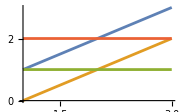

```mathematica
Plot[{x,x-1,1,2},{x,1,3}]
```

```mathematica
∫_1^2 (∫_1^x (x+2y)ⅆy)ⅆx+∫_2^3 (∫_(x-1)^2 (x+2y)ⅆy)ⅆx
```

5

Podemos ver el recinto desde otro punto de vista para simplificar los cálculos.

```mathematica
∫_1^2 (∫_y^(y+1) (x+2y)ⅆx)ⅆy
```

5

Calcular la integral de la función f(x,y)=Cos(x*y) en el recinto limitado por las rectas y=x/2, y=2x y el arco de la circunferencia centrado en (0,0) y que pasa  por los puntos (1,2) y (2,1).

```mathematica
∫_0^1 (∫_(x/2)^(2x) Cos[x*y ]ⅆy)ⅆx+∫_1^2 (∫_(x/2)^(√(5-x^2)) Cos[x*y ]ⅆy)ⅆx
```

∫_1^2 (-Sin[x^2/2]+Sin[x √(5-x^2)])/x ⅆx+1/2 (-SinIntegral[1/2]+SinIntegral[2])

Calcular la integral de la función x^2+y^2 en el recinto limitado por las circunferencias centradas en el (0,0) de radio 1 y 2, en el semiplano con y positiva.

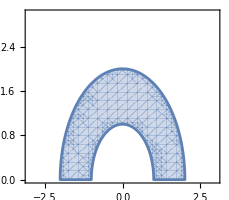

```mathematica
RegionPlot[1<=x^2+y^2<=4,{x,-3,3},{y,0,3}, AspectRatio->Automatic]
```